# Continuous frequency NMR signal

```mathematica
(* the freqeuncy distribution *)
f[ω_,ω0_,a_,b_]:= 1/(1+Exp[((ω-ω0)^2-a)/b])
```

```mathematica
Manipulate[Plot[f[ω,ω0,a,b],{ω,-10,10},PlotRange-> All],{ω0,0,6},{a,4,50},{b,0.1,10}]
```

```mathematica
g[x_,width_,pos_]:=((UnitStep[x-pos])(1-UnitStep[x-pos-width]))/2
```

```mathematica
Manipulate[Plot[g[x,w,p],{x,-5,5},PlotRange->All,Exclusions->None],{w,0.5,3},{p,0,4}]
```

```mathematica
(* forming signal from 2 delta frequency *)
```

```mathematica
Integrate[Cos[f[ω,ω0,a,b] t],ω]
```

∫Cos[t/(1+ⅇ^((-a+(ω-ω0)^2)/b))]ⅆω

```mathematica
S[t_]:=NIntegrate[Cos[f[ω,5,4,0.1] t],{ω,0,10}]
```

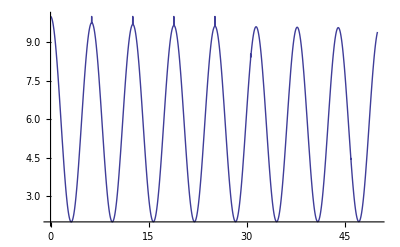

```mathematica
Plot[S[t],{t,0,50}]
```